```mathematica
F[x_]:=1/2 ⅈ (PolyLog[2,-ⅈ ⅇ^x]-PolyLog[2,ⅈ ⅇ^x])
```

```mathematica
G3[a_,b_]:=F[a-b]+F[b-a]-π/2(a+b);
```

```mathematica
EnergySetup[n_,FacesCW_]:=Module[{i,rhoV,rhoF,include,LineFaces,f,Faces,NM,nonlinefaces,radii,RADII},
Faces=Sort/@FacesCW;
f=Length[Faces];
LineFaces={};rhoV=Table[Subscript[rV, i],{i,1,n-2}];rhoF=Table[Subscript[rF, i],{i,1,f-2}];
include = {};
nonlinefaces={};
For[i=1,i≤f,i++,
If[!(Faces[[i,-2]]==n-1&&Faces[[i,-1]]==n),
(* then *) AppendTo[include,i];AppendTo[nonlinefaces,FacesCW[[i]]],
(* else *) AppendTo[LineFaces,i]]];

NM=NMinimize[{∑_(k=1)^(f-2) ∑_(i=1)^Length[Faces[[include[[k]]]]] If[Faces[[include[[k]],i]]<n-1,G3[Subscript[rV, Faces[[include[[k]],i]]],Subscript[rF, k]],0]+∑_(i=1)^(n-2) Subscript[rV, i] π If[MemberQ[Flatten@Table[Faces[[LineFaces[[m]]]],{m,1,2}],i],(* then *) 1,(* else *) 2]+∑_(j=1)^(f-2) Subscript[rF, j] π If[MemberQ[Faces[[include[[j]]]],n-1]||MemberQ[Faces[[include[[j]]]],n],(* then *) 1,(* else *) 2],
∑_(i=1)^(n-2) Subscript[rV, i]+∑_(j=1)^(f-2) Subscript[rF, j]==0},Join[rhoV,rhoF]];
RADII=Exp[Re[Join[rhoV,rhoF]/.(NM[[2]])]];
RADII/=RADII[[1]];
radii=<||>;
For[i=1,i≤n-2,i++,
radii[i]=RADII[[i]]
];
For[i=1,i≤Length[nonlinefaces],i++,
radii[nonlinefaces[[i]]]=RADII[[n-2+i]]
];
{radii,LineFaces}
];
```

```mathematica
Boundary[n_,FacesCW_,LineFaces_,radii_,ϵ_:0]:=Module[{i,j,faces,vertices,lastvisited,d,h,H,breaker,unvisited,f,endcircle,ComputeEndcircle,ComputeEndcircle2,delete},
unvisited =FacesCW;(*Keeps track of the faces we haven't visited*)
f=Length[FacesCW];

faces=<||>; (* centers of face circles (or normals, for lines) *)
For[i=1,i≤f,i++,faces[FacesCW[[i]]]={-∞,-∞}];
vertices=<||>; (* centers of vertex circles (or normals, for lines) *)
For[i=1,i≤n-2,i++,vertices[i]={-∞,-∞}];
(* Radii is an assoc from v->rad and facelist->rad *)

(*Vertex circles going vertically upwards along first FaceLine*)
h=0; (* height along the left line *)
For[i=1,i≤Length[FacesCW[[LineFaces[[1]]]]]-2(*Number of vertex circles that lie along first LineFace*),i++,
vertices[FacesCW[[LineFaces[[1]],i]]]={0,h+radii[FacesCW[[LineFaces[[1]],i]]]};(*Set the center of this vertex circle*)
h+=2radii[[FacesCW[[LineFaces[[1]],i]]]]];(*Keeps track of our cumulative height as we climb up the first FaceLine*)

unvisited=Delete[unvisited,Position[unvisited,FacesCW[[LineFaces[[1]]]]]];

d=0;(*Horizontal distance*)

ComputeEndcircle[prev_,face_]:=
(*Returns which vertex circle we calculated last based on previous vertex circle and face*)
If[face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n-1][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle[n,FacesCW[[LineFaces[[1]]]]];(*Previous vertex circle is bottom line, face is first FaceLine*)

(*Face circles going horizontally across upper vertex line*)
breaker=True;
For[j=1,j≤f ,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n-1], (*determine if this face-circle contains n-1, so it is on the upper vertex line*)
If[MemberQ[unvisited[[i]],ComputeEndcircle[endcircle,unvisited[[i]]]],
(*determine if this face-circle also contains the vertex right before n-1 to ensure we are going horizontally across in the right order*)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing--find the other face circle containing endcircle*)
,
(* else if the face circle is not a line*)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (*Set the center of this face circle*)
d+=2radii[unvisited[[i]]]; (* update how far along the top line we are *)
endcircle=ComputeEndcircle[endcircle,unvisited[[i]]];(*Update endcircle*)
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Vertex circles along the second FaceLine, climbing vertically upwards*)
h=0;
For[i=1,i≤Length[FacesCW[[LineFaces[[2]]]]]-2,i++,
vertices[FacesCW[[LineFaces[[2]],i]]]={d,h+radii[FacesCW[[LineFaces[[2]],i]]]};h+=2radii[[FacesCW[[LineFaces[[2]],i]]]]];
H=h;
h=0;(*Reset height*)

ComputeEndcircle2[prev_,face_]:=
If[face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle2[n-1,FacesCW[[LineFaces[[1]]]]];
(*Face circles along lower vertex line, moving horizontally from origin to second FaceLine*)
d=0;(*Reset distance*)
breaker=True;
For[j=1,j≤f,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n], (* determine if this face-circle contains n *)
If[MemberQ[unvisited[[i]],endcircle(* ComputeEndcircle2[endcircle,unvisited[[i]]] *)],(* determine if this face-cirlce also contains the vertex right before n *)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing*)
,
(* else *)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (* then we'll make this face's center be where we know it is *)
d+=2radii[unvisited[[i]]]; (* update how far along the bottom line we are *)
endcircle=ComputeEndcircle2[endcircle,unvisited[[i]]];
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Set the normals of the vertex lines and face lines*)
faces[FacesCW[[LineFaces[[2]]]]]={1,0};
faces[FacesCW[[LineFaces[[1]]]]]={-1,0};
vertices[n]={0,-1};
vertices[n-1]={0,1};

If[ThrowOrderError[faces,vertices,radii,d,H,n,FacesCW[[LineFaces]],0],
faces[FacesCW[[LineFaces[[1]]]]]*=-1;
faces[FacesCW[[LineFaces[[2]]]]]*=-1;
For[i=1,i≤n,i++,
If[i==n-1||i==n,
,
If[Abs[vertices[i][[1]]-d]≤ϵ,
vertices[i]={0,vertices[i][[2]]},
If[Abs[vertices[i][[1]]-0]≤ϵ,
vertices[i]={d,vertices[i][[2]]}]];
]]];

(*Return the assoc's of the faces to their centers and vertices to their centers*)
{vertices,faces,d,H}
];
```

```mathematica
FindRest[{x_,y_},r_,face_,vertices_,radii_,lines_]:=(* face is all the vertices that the face intersects *)
(*{x_,y_},r: known center of opposite kind and its radius
face: all the circles of its kind that pass thru that opposite known circle
vertices: all the circles of its kind that are tangent to the one we'e looking for*)
Module[{verts=vertices,i,j,ϕ,θ,ω,face2=face,b,b2=True},

If[verts[face2[[1]]]=={-∞,-∞}||MemberQ[lines,face2[[1]]],
For[i=2,i≤Length[face2]&&b2,i++,
If[verts[face2[[i]]]≠{-∞,-∞}&&!MemberQ[lines,face2[[i]]],
face2=Join[face2[[i;;]],face2[[;;i-1]]];
b2=False;
]]];

b=True;
For[i=2,i≤Length[face2]&&b,i++,
If[MemberQ[lines,face2[[i]]],
AppendTo[face2,face2[[1]]];
For[j=Length[face2]-1,j>i,j--,
If[verts[face2[[j]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[j+1]]][[1]]-x,verts[face2[[j+1]]][[2]]-y];
θ=ArcTan[radii[face2[[j+1]]]/r];(* j+1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[j]]]/r];
verts[face2[[j]]]={x+√(r^2+radii[face2[[j]]]^2)Cos[ϕ-θ-ω],y+√(r^2+radii[face2[[j]]]^2)Sin[ϕ-θ-ω]}
]
];b=False;Break,
If[verts[face2[[i]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[i-1]]][[1]]-x,verts[face2[[i-1]]][[2]]-y];
θ=ArcTan[radii[face2[[i-1]]]/r];(* i-1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[i]]]/r];
verts[face2[[i]]]={x+√(r^2+radii[face2[[i]]]^2)Cos[ϕ+θ+ω],y+√(r^2+radii[face2[[i]]]^2)Sin[ϕ+θ+ω]}];
];];
verts
];
```

```mathematica
Cull[assoc_]:=Module[{vis={},unv={},i},For[i=1,i≤Length[Keys[assoc]],i++,If[assoc[Keys[assoc][[i]]]=={-∞,-∞},AppendTo[unv,Keys[assoc][[i]]],AppendTo[vis,Keys[assoc][[i]]]]];{vis,unv}]
```

```mathematica
Interior[n_,FacesCW_,LineFaces_,radii_,vertices_,faces_,d_,h_]:=
Module[{Vunv={},Funv={},Vvis={},Fvis={},i,j,f,verts=vertices,verts2,fcs=faces,fcs2,fi,vi,x,y,k,b},
f=Length[FacesCW];
For[i=1,i≤n,i++,
If[vertices[i]=={-∞,-∞},AppendTo[Vunv,i],AppendTo[Vvis,i]]];
For[i=1,i≤f,i++,
If[faces[FacesCW[[i]]]=={-∞,-∞},AppendTo[Funv,FacesCW[[i]]],AppendTo[Fvis,FacesCW[[i]]]]];

For[j=1,j≤n+Length[FacesCW]&&(Length[Vunv]+Length[Funv]>0),j++,

For[i=1,i≤Length[Fvis],i++,(* for a known face circle *)
If[Length[Intersection[Vvis,Fvis[[i]]]]*Length[Intersection[Vunv,Fvis[[i]]]]>0,
fi=Fvis[[i]];
{x,y}=fcs[fi];
verts2=FindRest[{x,y},radii[fi],fi,verts,radii,{n-1,n}];
If[ThrowOrderError[fcs,verts2,radii,d,h,n,{FacesCW[[LineFaces[[1]]]],FacesCW[[LineFaces[[2]]]]},0],verts=FindRest[{x,y},radii[fi],Reverse[fi],verts,radii,{n-1,n}],
verts=verts2];
];
{Vvis,Vunv}=Cull[verts];
];

For[i=1,i≤Length[Vvis],i++, (* for a known vertex circle *)
If[b=False;
For[k=1,k≤Length[Fvis],k++,b=b||If[MemberQ[Fvis[[k]],Vvis[[i]]],True,False]];b,
If[b=False;For[k=1,k≤Length[Funv],k++,b=b||If[MemberQ[Funv[[k]],Vvis[[i]]],True,False]];b,
(* then *)
vi=Vvis[[i]];
{x,y}=verts[vi];
fcs2=FindRest[{x,y},radii[vi],FacesList[vi,FacesCW],fcs,radii,FacesCW[[LineFaces]]];
If[ThrowOrderError[fcs2,verts,radii,d,h,n,FacesCW[[LineFaces]],0],
fcs=FindRest[{x,y},radii[vi],
Reverse[FacesList[vi,FacesCW]],fcs,radii,FacesCW[[LineFaces]]],
fcs=fcs2];
];
{Fvis,Funv}=Cull[fcs];
]
];
];
{verts,fcs}
];
```

```mathematica
ThrowOrderError[fcs2_,verts_,radii_,d_,h_,n_,fls_,ϵ_](* fcs2 is proposed fcs association. fls is facelines *):=
Module[{i,j,b,b2,K},
K={};
For[i=1,i≤Length[Keys[fcs2]],i++,
If[!MemberQ[fls,Keys[fcs2][[i]]],AppendTo[K,Keys[fcs2][[i]]]]
];

b=False; (* "breaker" *)
For[i=1,i≤Length[K]&&!b,i++,
If[b2=False;
-∞<fcs2[K[[i]]][[1]]<0
||-∞<fcs2[K[[i]]][[2]]<0
||fcs2[K[[i]]][[1]]>d
||fcs2[K[[i]]][[2]]>h
||(For[j=1,j≤Length[K[[i]]],j++,
If[K[[i,j]]≠n-1&&K[[i,j]]≠n&&verts[K[[i,j]]]≠{-∞,-∞}&&fcs2[K[[i]]]≠{-∞,-∞},
If[EuclideanDistance[verts[K[[i,j]]],fcs2[K[[i]]]]≥(1-ϵ)(radii[K[[i,j]]]+radii[K[[i]]]),b2=True;Break]]];b2),
b=True,

For[j=1,j≤Length[K]&&!b,j++,
If[i≠j&&fcs2[K[[i]]]≠{-∞,-∞}&&fcs2[K[[j]]]≠{-∞,-∞}&&
EuclideanDistance[fcs2[K[[i]]],fcs2[K[[j]]]]<(1+ϵ)(radii[fcs2[K[[i]]]]+radii[fcs2[K[[j]]]])
,(* then, bad *) b=True]]];
];


For[i=1,i≤Length[fls[[1]]]&&!b,i++,
If[verts[fls[[1,i]]][[1]]≠d/2+fcs2[fls[[1]]][[1]] d/2&&fls[[1,i]]<n-1,b=True]
];
For[i=1,i≤Length[fls[[2]]]&&!b,i++,
If[verts[fls[[2,i]]][[1]]≠d/2+fcs2[fls[[2]]][[1]] d/2&&fls[[2,i]]<n-1,b=True]
];

b
];
```

```mathematica
FacesList[v_,Faces_]:=
Module[{ContainV={},i,L=2,p=3,temp},
For[i=1,i≤Length[Faces],i++,
If[MemberQ[Faces[[i]],v],AppendTo[ContainV,Faces[[i]]]]];
While[L<Length[ContainV],
While[p≤Length[ContainV],
If[Length[Intersection[ContainV[[L-1]],ContainV[[p]]]]==2,
temp=ContainV[[p]];ContainV[[p]]=ContainV[[L]];ContainV[[L]]=temp;p=1+Length[ContainV],
p++]
];
L++;
p=L+1;
];
ContainV];
```

```mathematica
Q=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
InvCoords[z_,r_,d_:0]:=If[r==∞,{2d,0,z},{Norm[z]^2/r-r,1/r,z/r}];
```

```mathematica
Gram[SC_]:=SC.Q.Transpose[SC];
SuperCluster[vertices_,faces_,radii_,fls_,d_,h_,n_]:=
Module[{sc={},i},
For[i=1,i≤n-2,i++,AppendTo[sc,Flatten[InvCoords[vertices[i],radii[i]]]]];
AppendTo[sc,Flatten[InvCoords[vertices[n-1],∞,h/2+vertices[n-1][[2]] h/2]]];
AppendTo[sc,Flatten[InvCoords[vertices[n],∞,h/2+vertices[n][[2]] h/2]]];
For[i=1,i≤Length[Keys[faces]],i++,
If[!MemberQ[fls,Keys[faces][[i]]],
AppendTo[sc,Flatten[InvCoords[faces[Keys[faces][[i]]],radii[Keys[faces][[i]]]]]]
]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[1]]],∞,d/2+faces[fls[[1]]][[1]] d/2]]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[2]]],∞,d/2+faces[fls[[2]]][[1]] d/2]]];
sc
];
```

```mathematica
DrawCircle[{bhat_,b_,bx_,by_}]:=If[Abs[b]≥ .01,Circle[{bx,by}/b,1/b],InfiniteLine[{bx,by}bhat/2,{-by,bx}]];
```

```mathematica
Packing[n_,FacesCW_,ϵ_:0]:=
Module[{radii,LineFaces,vertices,faces,d,h},
{radii,LineFaces}=EnergySetup[n,FacesCW];
{vertices,faces,d,h}=Boundary[n,FacesCW,LineFaces,radii,ϵ];
{vertices,faces}=Interior[n,FacesCW,LineFaces,radii,vertices,faces,d,h];
{vertices,faces,radii,d,h,LineFaces}];
```

```mathematica
Render[radii_,fcs_,verts_,fls_,n_,d_,h_]:=Graphics[{Blue,Thick,
Table[If[i==n-1,Line[{{-Max[Values[radii]],h},{d+Max[Values[radii]],h}}],If[i==n,Line[{{-Max[Values[radii]],0},{d+Max[Values[radii]],0}}],
Circle[verts[Keys[verts][[i]]],radii[Keys[verts][[i]]]]]],{i,1,n}],
Red,Dashed,
Table[If[Keys[fcs][[i]]==fls[[1]],Line[{{0,-Max[Values[radii]]},{0,h+Max[Values[radii]]}}],
If[Keys[fcs][[i]]==fls[[2]],Line[{{d,-Max[Values[radii]]},{d,h+Max[Values[radii]]}}],
Circle[fcs[Keys[fcs][[i]]],radii[Keys[fcs][[i]]]]]],{i,1,Length[Keys[fcs]]}]
}];
```

```mathematica
SendToInt[ϵ_:0][y_]:=With[{x=Simplify[y]},If[Abs[x-Floor[x]]≤ϵ ,Floor[x],
If[Abs[x-Ceiling[x]]≤ ϵ ,Ceiling[x],x],x]];
```

```mathematica
R[vhat_]:=IdentityMatrix[4]+2Q.Transpose[{vhat}].{vhat}
BMat[n_]:=Table[b[i,j],{i,1,n},{j,1,n}];

Bend[V_,m_][i_]:=
Module[{sol,assignments,rest,l,others1,others2},
sol=Solve[BMat[m].(V[[;;m]])==(V[[;;m]]).R[V[[m+i]]]][[1]];
assignments=Association[sol];
rest=Complement[Flatten[BMat[m]],Keys[assignments]];
l=Length[rest];
others1=Solve[rest==Table[0,{j,1,l}]][[1]];
others2=<||>;
For[j=1,j≤l,j++,others2[rest[[j]]]=Subscript[a, j]];
others2=Normal[others2];
Column[{
MatrixForm[(BMat[m]/.assignments)/.others2],
MatrixForm[(BMat[m]/.assignments)/.others1]
}]
];
```

```mathematica
Everything[n_,FacesCW_,ϵ_:0,steps_,sizemax_:∞]:=Module[{vertices,faces,f=Length[FacesCW],radii,d,h,LineFaces,Vnye,Vout,bends={}},
{vertices,faces,radii,d,h,LineFaces}=Packing[n,FacesCW,ϵ];
Vnye=SendToInt[ϵ]//@SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n];
Vout=MatrixForm[Simplify[RootApproximant[Vnye]]];
bends=Bend[Vout[[1]],n]/@Range@f;
Column[{
Render[radii,faces,vertices,FacesCW[[LineFaces]],n,d,h],
Graphics[{Thick, DrawCircle/@Orbit[Vnye[[-f;;]],Vnye[[;;n]],steps,sizemax],Red,DrawCircle/@Vnye[[-f;;]], Blue, DrawCircle/@Vnye[[;;n]]},PlotRange->{{-d,2 d},{-1.2 Max[Values[radii]],h+1.2 Max[Values[radii]]}},PlotRangeClipping->True],
Vout,
bends,
MatrixForm[Simplify[RootApproximant[
SendToInt[ϵ]//@Gram[SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n]]]
]]
}]]
```

```mathematica
Orbit[co_,cl_,steps_,sizemax_:∞]:=Module[{i,j,k,orbit=cl,L},
For[i=1,i≤steps,i++,
L=Length[orbit];
For[j=1,j≤Length[co],j++,
For[k=1,k≤L,k++,
If[(orbit⟦k⟧.R[co⟦j⟧])⟦2⟧≤sizemax&&!MemberQ[Round[N[orbit],.001],Round[N[orbit⟦k⟧.R[co⟦j⟧]],.001](*new thing*)],AppendTo[orbit,orbit⟦k⟧.R[co⟦j⟧](*newthing*)]]
]
]
];
orbit
];
```

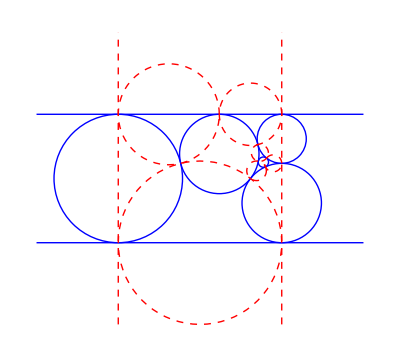
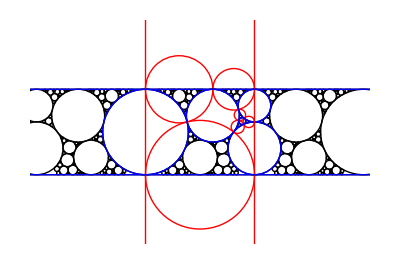
-Graphics-
-Graphics-
(8+4 √5 | 1 | Root[-16-16 #1^2+#1^4&,2] | 1
20+8 √5 | 1/2 (1+√5) | Root[-16-44 #1^2+#1^4&,2] | 2+√5
Root[-184+122 #1-271 #1^2+2 #1^3&,1] | Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] | Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]
6+2 √5 | 1 | Root[-16-4 #1^2+#1^4&,2] | √5
0 | 1/2 (-1+√5) | 0 | 1
2+2 √5 | 0 | 0 | 1
0 | 0 | 0 | -1
0 | Root[-1+4 #1^2+#1^4&,2] | 1 | 0
Root[-256-64 #1^2+#1^4&,2] | Root[-1+#1^2+#1^4&,2] | 1 | Root[-16-4 #1^2+#1^4&,2]
Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4] | Root[-1-#1^2+#1^4&,2] | 2+√5 | Root[-16-16 #1^2+#1^4&,2]
Root[3659-73 #1-832 #1^2+10 #1^3&,3] | Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2] | 1/299 (2266+42 √4195) | Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]
Root[5374-16 #1-188 #1^2+3 #1^3&,3] | Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2] | Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] | Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]
Root[-129+462 #1-64 #1^2-717 #1^3+8 #1^4&,4] | Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2] | Root[-139-212 #1-102 #1^2-12 #1^3+#1^4&,2] | Root[16-32 #1+28 #1^2-12 #1^3+#1^4&,2]
Root[-256-64 #1^2+#1^4&,2] | 0 | 1 | 0
0 | 0 | -1 | 0)
{(a_1 | a_2 | -(Root[-16-16 #1^2+#1^4&,2]-(8+4 √5) Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_1)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_2)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_3)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_3 | (2 (Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-16 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-1+4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[-1+4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+√5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_1)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+20 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_2)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+6 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_3)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+12 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-112 Root[-1+4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-48 √5 Root[-1+4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-64 Root[-1+4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-32 √5 Root[-1+4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+112 Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+48 √5 Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+16 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-44 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
a_4 | a_5 | -(Root[-16-44 #1^2+#1^4&,2]-(20+8 √5) Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_4)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_5)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_6)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_6 | -(-1-√5+4 Root[-16-44 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2]-40 Root[-1+4 #1^2+#1^4&,2]^2-16 √5 Root[-1+4 #1^2+#1^4&,2]^2)/(-1+√5)+(2 (Root[-16-44 #1^2+#1^4&,2]-(20+8 √5) Root[-1+4 #1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | (2 (5+2 √5))/(1+√5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (Root[-16-44 #1^2+#1^4&,2]-(20+8 √5) Root[-1+4 #1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | -(-3-√5)/(1+√5)-(-1-√5+4 Root[-16-44 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2]-40 Root[-1+4 #1^2+#1^4&,2]^2-16 √5 Root[-1+4 #1^2+#1^4&,2]^2)/(-1+√5)+((Root[-16-44 #1^2+#1^4&,2]-(20+8 √5) Root[-1+4 #1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_4-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_5-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_6
a_7 | a_8 | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_7)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_8)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_9)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_9 | (2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]^2-2 Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_7-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_8-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_9 | -(Root[-184+122 #1-271 #1^2+2 #1^3&,1]^2 Root[-1+4 #1^2+#1^4&,2]-2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_7-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_8-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_9 | Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 (Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]^2-2 Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(-1+√5)+((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_7-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_8-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_9
a_10 | a_11 | -(Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_10)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_11)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_12)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_12 | -(2 (-1+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]^2))/(-1+√5)+(2 (Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_10-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_11-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_12 | -(-3-√5)/(1+√5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_10-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_11-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_12 | -2/(1+√5)-(2 (-1+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]^2))/(-1+√5)+((Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_10-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_11-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_12
a_13 | a_14 | -(Root[-16-16 #1^2+#1^4&,2] a_13)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_14)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_15)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_15 | 1-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_13-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_14-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_15 | -((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_13-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_14-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_15 | -(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_13-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_14-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_15
a_16 | a_17 | (2 (1+√5) Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_16)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_17)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_18)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_18 | (4 (1+√5) Root[-1+4 #1^2+#1^4&,2]^2)/(-1+√5)-(4 (1+√5) Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_16-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_17-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_18 | 1-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_16-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_17-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_18 | (4 (1+√5) Root[-1+4 #1^2+#1^4&,2]^2)/(-1+√5)-(2 (1+√5) Root[-1+4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_16-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_17-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_18
a_19 | a_20 | -(Root[-16-16 #1^2+#1^4&,2] a_19)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_20)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_21)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_21 | -(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_19-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_20-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_21 | -((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_19-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_20-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_21 | 1-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_19-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_20-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_21)
(0 | 0 | -(Root[-16-16 #1^2+#1^4&,2]-(8+4 √5) Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 (Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-16 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-1+4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[-1+4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+12 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-112 Root[-1+4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-48 √5 Root[-1+4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-64 Root[-1+4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-32 √5 Root[-1+4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+112 Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+48 √5 Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
0 | 0 | -(Root[-16-44 #1^2+#1^4&,2]-(20+8 √5) Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(-1-√5+4 Root[-16-44 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2]-40 Root[-1+4 #1^2+#1^4&,2]^2-16 √5 Root[-1+4 #1^2+#1^4&,2]^2)/(-1+√5)+(2 (Root[-16-44 #1^2+#1^4&,2]-(20+8 √5) Root[-1+4 #1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | (2 (5+2 √5))/(1+√5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (Root[-16-44 #1^2+#1^4&,2]-(20+8 √5) Root[-1+4 #1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-3-√5)/(1+√5)-(-1-√5+4 Root[-16-44 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2]-40 Root[-1+4 #1^2+#1^4&,2]^2-16 √5 Root[-1+4 #1^2+#1^4&,2]^2)/(-1+√5)+((Root[-16-44 #1^2+#1^4&,2]-(20+8 √5) Root[-1+4 #1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]
0 | 0 | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]^2-2 Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(-1+√5) | -(Root[-184+122 #1-271 #1^2+2 #1^3&,1]^2 Root[-1+4 #1^2+#1^4&,2]-2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 (Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]^2-2 Root[-1+4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(-1+√5)+((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]
0 | 0 | -(Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(2 (-1+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]^2))/(-1+√5)+(2 (Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-3-√5)/(1+√5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -2/(1+√5)-(2 (-1+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]^2))/(-1+√5)+((Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+4 #1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | (2 (1+√5) Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (4 (1+√5) Root[-1+4 #1^2+#1^4&,2]^2)/(-1+√5)-(4 (1+√5) Root[-1+4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | 1-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | (4 (1+√5) Root[-1+4 #1^2+#1^4&,2]^2)/(-1+√5)-(2 (1+√5) Root[-1+4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]
0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | a_2 | -(-Root[-256-64 #1^2+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]-(8+4 √5) Root[-1+#1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_1)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_2)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_3)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_3 | (2 (Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-16 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-1+#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[-1+#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 Root[-1+#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-1+#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+√5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-256-64 #1^2+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+8 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_1)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+20 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_2)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+6 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_3)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-256-64 #1^2+#1^4&,2]+√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-256-64 #1^2+#1^4&,2]+Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]-2 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+12 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-256-64 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-√5 Root[-256-64 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-256-64 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[-256-64 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+6 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-16 Root[-16-16 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-16 Root[-16-4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-16 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+72 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+40 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-112 Root[-1+#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-48 √5 Root[-1+#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 Root[-256-64 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+16 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-64 Root[-1+#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-32 √5 Root[-1+#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+4 Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+4 √5 Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 √5 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+112 Root[-1+#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+48 √5 Root[-1+#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+16 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-44 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
a_4 | a_5 | -(-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]+Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_4)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_5)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_6)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_6 | -(2 (2 Root[-16-44 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2]^2-1/2 (1+√5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])))/(-1+√5)+(2 (-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]+Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | -(-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]^2+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]))/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]+Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | -(-8-4 √5-Root[-256-64 #1^2+#1^4&,2]^2-Root[-256-64 #1^2+#1^4&,2] Root[-16-44 #1^2+#1^4&,2]+√5 Root[-256-64 #1^2+#1^4&,2] Root[-16-44 #1^2+#1^4&,2]+5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]+3 √5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-8 Root[-16-44 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-16 Root[-16-4 #1^2+#1^4&,2]^2-8 √5 Root[-16-4 #1^2+#1^4&,2]^2-16 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-8 √5 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+4 Root[-16-44 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+4 √5 Root[-16-44 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+108 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+44 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-120 Root[-1+#1^2+#1^4&,2]^2-56 √5 Root[-1+#1^2+#1^4&,2]^2)/((-1+√5) (1+√5))+((-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]+Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_4-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_5-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_6
a_7 | a_8 | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_7)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_8)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_9)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_9 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]^2+2 Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_7-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_8-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_9 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])+2 Root[-256-64 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_7-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_8-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_9 | -Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]^2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])+2 Root[-256-64 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(2+2 √5)-(2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]^2+2 Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(-1+√5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_7-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_8-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_9
a_10 | a_11 | -(-Root[-256-64 #1^2+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_10)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_11)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_12)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_12 | -(2 (-1-Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2]^2))/(-1+√5)+(2 (-Root[-256-64 #1^2+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_10-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_11-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_12 | -(-Root[-256-64 #1^2+#1^4&,2]^2+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]))/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-Root[-256-64 #1^2+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_10-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_11-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_12 | -(-8+Root[-256-64 #1^2+#1^4&,2]^2-√5 Root[-256-64 #1^2+#1^4&,2]^2+16 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-16 Root[-16-4 #1^2+#1^4&,2]^2-16 √5 Root[-16-4 #1^2+#1^4&,2]^2-8 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-8 √5 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+96 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+32 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-64 Root[-1+#1^2+#1^4&,2]^2-32 √5 Root[-1+#1^2+#1^4&,2]^2)/(2 (-1+√5) (1+√5))+((-Root[-256-64 #1^2+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_10-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_11-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_12
a_13 | a_14 | -(-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_13)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_14)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_15)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_15 | -(2 (2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-1/2 (-1+√5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])))/(-1+√5)+(2 (-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_13-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_14-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_15 | -(-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]^2+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2])/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_13-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_14-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_15 | -(4+4 √5+Root[-256-64 #1^2+#1^4&,2]^2-√5 Root[-256-64 #1^2+#1^4&,2]^2+12 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-8 Root[-16-4 #1^2+#1^4&,2]^2-8 √5 Root[-16-4 #1^2+#1^4&,2]^2)/(4 (1+√5))-(2 (2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-1/2 (-1+√5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])))/(-1+√5)+((-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_13-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_14-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_15
a_16 | a_17 | -(2 Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_16)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_17)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_18)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_18 | -(2 (2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2]^2))/(-1+√5)+(2 (2 Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_16-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_17-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_18 | -(2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]))/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (2 Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_16-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_17-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_18 | -(-Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]+√5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-8 Root[-16-4 #1^2+#1^4&,2]^2-4 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+12 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+12 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-24 Root[-1+#1^2+#1^4&,2]^2-8 √5 Root[-1+#1^2+#1^4&,2]^2)/((-1+√5) (1+√5))+((2 Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_16-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_17-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_18
a_19 | a_20 | (2 Root[-16-4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_19)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_20)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_21)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_21 | (4 Root[-16-4 #1^2+#1^4&,2] (Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_19-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_20-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_21 | (Root[-16-4 #1^2+#1^4&,2] (-Root[-184+122 #1-271 #1^2+2 #1^3&,1]+Root[-256-64 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]))/((1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_19-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_20-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_21 | 1+(Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2])/(1+√5)-2 Root[-16-4 #1^2+#1^4&,2]^2+(4 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_19-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_20-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_21)
(0 | 0 | -(-Root[-256-64 #1^2+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]-(8+4 √5) Root[-1+#1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 (Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-16 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-1+#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[-1+#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 Root[-1+#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-1+#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-256-64 #1^2+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+8 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-256-64 #1^2+#1^4&,2]+√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-256-64 #1^2+#1^4&,2]+Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]-2 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+12 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-256-64 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-√5 Root[-256-64 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-256-64 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[-256-64 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+6 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-16 Root[-16-16 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-16 Root[-16-4 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-16 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+72 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+40 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-112 Root[-1+#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-48 √5 Root[-1+#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 Root[-256-64 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+16 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-64 Root[-1+#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-32 √5 Root[-1+#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+4 Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+4 √5 Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 √5 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+112 Root[-1+#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+48 √5 Root[-1+#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
0 | 0 | -(-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]+Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(2 (2 Root[-16-44 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2]^2-1/2 (1+√5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])))/(-1+√5)+(2 (-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]+Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]^2+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]))/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]+Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-8-4 √5-Root[-256-64 #1^2+#1^4&,2]^2-Root[-256-64 #1^2+#1^4&,2] Root[-16-44 #1^2+#1^4&,2]+√5 Root[-256-64 #1^2+#1^4&,2] Root[-16-44 #1^2+#1^4&,2]+5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]+3 √5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-8 Root[-16-44 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-16 Root[-16-4 #1^2+#1^4&,2]^2-8 √5 Root[-16-4 #1^2+#1^4&,2]^2-16 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-8 √5 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+4 Root[-16-44 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+4 √5 Root[-16-44 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+108 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+44 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-120 Root[-1+#1^2+#1^4&,2]^2-56 √5 Root[-1+#1^2+#1^4&,2]^2)/((-1+√5) (1+√5))+((-1/2 (1+√5) Root[-256-64 #1^2+#1^4&,2]+Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[-16-4 #1^2+#1^4&,2]-(20+8 √5) Root[-1+#1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]
0 | 0 | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]^2+2 Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])+2 Root[-256-64 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(2+2 √5) | -Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]^2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])+2 Root[-256-64 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-256-64 #1^2+#1^4&,2]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(2+2 √5)-(2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1+#1^2+#1^4&,2]^2+2 Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/(-1+√5)
0 | 0 | -(-Root[-256-64 #1^2+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(2 (-1-Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2]^2))/(-1+√5)+(2 (-Root[-256-64 #1^2+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-Root[-256-64 #1^2+#1^4&,2]^2+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]))/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-Root[-256-64 #1^2+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-8+Root[-256-64 #1^2+#1^4&,2]^2-√5 Root[-256-64 #1^2+#1^4&,2]^2+16 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-16 Root[-16-4 #1^2+#1^4&,2]^2-16 √5 Root[-16-4 #1^2+#1^4&,2]^2-8 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-8 √5 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+96 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+32 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-64 Root[-1+#1^2+#1^4&,2]^2-32 √5 Root[-1+#1^2+#1^4&,2]^2)/(2 (-1+√5) (1+√5))+((-Root[-256-64 #1^2+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-4 #1^2+#1^4&,2]-(6+2 √5) Root[-1+#1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]
0 | 0 | -(-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(2 (2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-1/2 (-1+√5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])))/(-1+√5)+(2 (-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]^2+2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2])/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(4+4 √5+Root[-256-64 #1^2+#1^4&,2]^2-√5 Root[-256-64 #1^2+#1^4&,2]^2+12 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-8 Root[-16-4 #1^2+#1^4&,2]^2-8 √5 Root[-16-4 #1^2+#1^4&,2]^2)/(4 (1+√5))-(2 (2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-1/2 (-1+√5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])))/(-1+√5)+((-1/2 (-1+√5) Root[-256-64 #1^2+#1^4&,2]+2 Root[-16-4 #1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]
0 | 0 | -(2 Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(2 (2 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2]^2))/(-1+√5)+(2 (2 Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(2 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) (1+Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]))/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (2 Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]+√5 Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-8 Root[-16-4 #1^2+#1^4&,2]^2-4 Root[-256-64 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+12 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]+12 √5 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2]-24 Root[-1+#1^2+#1^4&,2]^2-8 √5 Root[-1+#1^2+#1^4&,2]^2)/((-1+√5) (1+√5))+((2 Root[-16-4 #1^2+#1^4&,2]-(2+2 √5) Root[-1+#1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]
0 | 0 | (2 Root[-16-4 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (4 Root[-16-4 #1^2+#1^4&,2] (Root[-1+#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | (Root[-16-4 #1^2+#1^4&,2] (-Root[-184+122 #1-271 #1^2+2 #1^3&,1]+Root[-256-64 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]))/((1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | 1+(Root[-256-64 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2])/(1+√5)-2 Root[-16-4 #1^2+#1^4&,2]^2+(4 Root[-16-4 #1^2+#1^4&,2] Root[-1+#1^2+#1^4&,2])/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]),(a_1 | a_2 | -(2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-16 #1^2+#1^4&,2]-(2+√5) (8+4 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_1)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_2)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_3)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_3 | -(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+6 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 Root[-1-#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[-1-#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-21 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-10 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+36 Root[-1-#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+16 √5 Root[-1-#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+√5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+√5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-21 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-10 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+36 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]+16 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+6 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-8 Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-4 √5 Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_1)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+20 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_2)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+6 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_3)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-29 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-11 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+44 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]+20 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-48 Root[-16-16 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-16 √5 Root[-16-16 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+128 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+64 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-112 Root[-1-#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-48 √5 Root[-1-#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+168 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+80 √5 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-288 Root[-1-#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-128 √5 Root[-1-#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-284 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-124 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+464 Root[-1-#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+208 √5 Root[-1-#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+3 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+12 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+4 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-16 Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-8 √5 Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-16 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-8 √5 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+28 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+12 √5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-√5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+16 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-44 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
a_4 | a_5 | -(-(1+2 (-2-√5) (2+√5)) Root[-16-44 #1^2+#1^4&,2]+2 (2+√5)^2 Root[-16-16 #1^2+#1^4&,2]-(2+√5) (20+8 √5) Root[-1-#1^2+#1^4&,2]-1/2 (1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_4)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_5)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_6)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_6 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-(1+2 (-2-√5) (2+√5)) Root[-16-44 #1^2+#1^4&,2]+2 (2+√5)^2 Root[-16-16 #1^2+#1^4&,2]-(2+√5) (20+8 √5) Root[-1-#1^2+#1^4&,2]-1/2 (1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-2 (-2-√5) Root[-16-44 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(20+8 √5) Root[-1-#1^2+#1^4&,2]^2-1/2 (1+√5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-(1+2 (-2-√5) (2+√5)) Root[-16-44 #1^2+#1^4&,2]+2 (2+√5)^2 Root[-16-16 #1^2+#1^4&,2]-(2+√5) (20+8 √5) Root[-1-#1^2+#1^4&,2]-1/2 (1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-2 (-2-√5) Root[-16-44 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-1/2 (1+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-(20+8 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-(1+2 (-2-√5) (2+√5)) Root[-16-44 #1^2+#1^4&,2]+2 (2+√5)^2 Root[-16-16 #1^2+#1^4&,2]-(2+√5) (20+8 √5) Root[-1-#1^2+#1^4&,2]-1/2 (1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(-8-4 √5-16 Root[-16-44 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2]-8 √5 Root[-16-44 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2]-16 Root[-16-16 #1^2+#1^4&,2]^2-8 √5 Root[-16-16 #1^2+#1^4&,2]^2+28 Root[-16-44 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+12 √5 Root[-16-44 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+108 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+44 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-120 Root[-1-#1^2+#1^4&,2]^2-56 √5 Root[-1-#1^2+#1^4&,2]^2+3 Root[-16-44 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+√5 Root[-16-44 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+5 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+3 √5 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-16 Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-8 √5 Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/((-1+√5) (1+√5))-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_4-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_5-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_6
a_7 | a_8 | -(-(2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(2+√5) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_7)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_8)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_9)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_9 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-(2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(2+√5) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]^2-2 (-2-√5) Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_7-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_8-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_9 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-(2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(2+√5) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-2 (-2-√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_7-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_8-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_9 | -Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+4 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+2 Root[-16-16 #1^2+#1^4&,2]^2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-(2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(2+√5) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(-2 (-2-√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)-(2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]^2-2 (-2-√5) Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_7-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_8-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_9
a_10 | a_11 | -(2 √5 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-4 #1^2+#1^4&,2]-(2+√5) (6+2 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_10)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_11)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_12)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_12 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (2 √5 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-4 #1^2+#1^4&,2]-(2+√5) (6+2 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-1+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-2 (-2-√5) Root[-16-4 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(6+2 √5) Root[-1-#1^2+#1^4&,2]^2-Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_10-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_11-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_12 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (2 √5 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-4 #1^2+#1^4&,2]-(2+√5) (6+2 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-2 (-2-√5) Root[-16-4 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-(6+2 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_10-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_11-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_12 | -√5+2 √5 Root[-16-16 #1^2+#1^4&,2]^2+4 Root[-16-16 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-6 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (2 √5 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-4 #1^2+#1^4&,2]-(2+√5) (6+2 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(2 (-1+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-2 (-2-√5) Root[-16-4 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(6+2 √5) Root[-1-#1^2+#1^4&,2]^2-Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(-1+√5)-(2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-2 (-2-√5) Root[-16-4 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-(6+2 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_10-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_11-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_12
a_13 | a_14 | -(2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-1/2 (-1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_13)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_14)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_15)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_15 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-1/2 (-1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-1/2 (-1+√5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_13-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_14-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_15 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-1/2 (-1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-1/2 (-1+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_13-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_14-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_15 | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-1/2 (-1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4+4 √5-8 Root[-16-16 #1^2+#1^4&,2]^2-8 √5 Root[-16-16 #1^2+#1^4&,2]^2+12 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-√5 Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/(4 (1+√5))-(2 (2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-1/2 (-1+√5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_13-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_14-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_15
a_16 | a_17 | (2 (2+√5) (-Root[-16-16 #1^2+#1^4&,2]+Root[-1-#1^2+#1^4&,2]+√5 Root[-1-#1^2+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_16)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_17)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_18)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_18 | -(2 (2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(2+2 √5) Root[-1-#1^2+#1^4&,2]^2))/(-1+√5)-(4 (2+√5) (-Root[-16-16 #1^2+#1^4&,2]+Root[-1-#1^2+#1^4&,2]+√5 Root[-1-#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_16-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_17-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_18 | -((2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-Root[-16-16 #1^2+#1^4&,2]+Root[-1-#1^2+#1^4&,2]+√5 Root[-1-#1^2+#1^4&,2]))/((1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-(2+2 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_16-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_17-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_18 | -1+2 Root[-16-16 #1^2+#1^4&,2]^2-2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(2 (2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(2+2 √5) Root[-1-#1^2+#1^4&,2]^2))/(-1+√5)-(2 (2+√5) (-Root[-16-16 #1^2+#1^4&,2]+Root[-1-#1^2+#1^4&,2]+√5 Root[-1-#1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(2 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-(2+2 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_16-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_17-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_18
a_19 | a_20 | (2 (2+√5) Root[-16-16 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_19)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_20)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_21)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_21 | (4 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2])/(-1+√5)-(4 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_19-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_20-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_21 | -((2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/((1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/(1+√5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_19-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_20-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_21 | 1-2 Root[-16-16 #1^2+#1^4&,2]^2+(4 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2])/(-1+√5)-(2 (2+√5) Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+(Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/(1+√5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_19-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_20-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_21)
(0 | 0 | -(2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-16 #1^2+#1^4&,2]-(2+√5) (8+4 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+6 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 Root[-1-#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[-1-#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-21 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-10 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+36 Root[-1-#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+16 √5 Root[-1-#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+√5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-21 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-10 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+36 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]+16 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+6 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-8 Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-4 √5 Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-29 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-11 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+44 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]+20 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-48 Root[-16-16 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-16 √5 Root[-16-16 #1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+128 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+64 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-112 Root[-1-#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-48 √5 Root[-1-#1^2+#1^4&,2]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+168 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+80 √5 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-288 Root[-1-#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-128 √5 Root[-1-#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-284 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-124 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+464 Root[-1-#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+208 √5 Root[-1-#1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+3 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+12 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+4 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-16 Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-8 √5 Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-16 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-8 √5 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+28 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+12 √5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-√5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
0 | 0 | -(-(1+2 (-2-√5) (2+√5)) Root[-16-44 #1^2+#1^4&,2]+2 (2+√5)^2 Root[-16-16 #1^2+#1^4&,2]-(2+√5) (20+8 √5) Root[-1-#1^2+#1^4&,2]-1/2 (1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-(1+2 (-2-√5) (2+√5)) Root[-16-44 #1^2+#1^4&,2]+2 (2+√5)^2 Root[-16-16 #1^2+#1^4&,2]-(2+√5) (20+8 √5) Root[-1-#1^2+#1^4&,2]-1/2 (1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-2 (-2-√5) Root[-16-44 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(20+8 √5) Root[-1-#1^2+#1^4&,2]^2-1/2 (1+√5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-(1+2 (-2-√5) (2+√5)) Root[-16-44 #1^2+#1^4&,2]+2 (2+√5)^2 Root[-16-16 #1^2+#1^4&,2]-(2+√5) (20+8 √5) Root[-1-#1^2+#1^4&,2]-1/2 (1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-2 (-2-√5) Root[-16-44 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-1/2 (1+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-(20+8 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5) | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-(1+2 (-2-√5) (2+√5)) Root[-16-44 #1^2+#1^4&,2]+2 (2+√5)^2 Root[-16-16 #1^2+#1^4&,2]-(2+√5) (20+8 √5) Root[-1-#1^2+#1^4&,2]-1/2 (1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(-8-4 √5-16 Root[-16-44 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2]-8 √5 Root[-16-44 #1^2+#1^4&,2] Root[-16-16 #1^2+#1^4&,2]-16 Root[-16-16 #1^2+#1^4&,2]^2-8 √5 Root[-16-16 #1^2+#1^4&,2]^2+28 Root[-16-44 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+12 √5 Root[-16-44 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+108 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+44 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-120 Root[-1-#1^2+#1^4&,2]^2-56 √5 Root[-1-#1^2+#1^4&,2]^2+3 Root[-16-44 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+√5 Root[-16-44 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+5 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+3 √5 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-16 Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-8 √5 Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/((-1+√5) (1+√5))
0 | 0 | -(-(2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(2+√5) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-(2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(2+√5) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]^2-2 (-2-√5) Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-(2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(2+√5) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-2 (-2-√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5) | -Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]+4 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+2 Root[-16-16 #1^2+#1^4&,2]^2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-(2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-(2+√5) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(-2 (-2-√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+2 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)-(2 (-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-1-#1^2+#1^4&,2]^2-2 (-2-√5) Root[-1-#1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5)
0 | 0 | -(2 √5 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-4 #1^2+#1^4&,2]-(2+√5) (6+2 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (2 √5 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-4 #1^2+#1^4&,2]-(2+√5) (6+2 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-1+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-2 (-2-√5) Root[-16-4 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(6+2 √5) Root[-1-#1^2+#1^4&,2]^2-Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (2 √5 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-4 #1^2+#1^4&,2]-(2+√5) (6+2 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-2 (-2-√5) Root[-16-4 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-(6+2 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5) | -√5+2 √5 Root[-16-16 #1^2+#1^4&,2]^2+4 Root[-16-16 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-16-4 #1^2+#1^4&,2]-6 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (2 √5 (2+√5) Root[-16-16 #1^2+#1^4&,2]-(1+2 (-2-√5) (2+√5)) Root[-16-4 #1^2+#1^4&,2]-(2+√5) (6+2 √5) Root[-1-#1^2+#1^4&,2]-(2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(2 (-1+2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-2 (-2-√5) Root[-16-4 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(6+2 √5) Root[-1-#1^2+#1^4&,2]^2-Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(-1+√5)-(2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-2 (-2-√5) Root[-16-4 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-(6+2 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)
0 | 0 | -(2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-1/2 (-1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-1/2 (-1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-1/2 (-1+√5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-1/2 (-1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-1/2 (-1+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/(2+2 √5) | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (2 (2+√5) Root[-16-16 #1^2+#1^4&,2]-1/2 (-1+√5) (2+√5) Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4+4 √5-8 Root[-16-16 #1^2+#1^4&,2]^2-8 √5 Root[-16-16 #1^2+#1^4&,2]^2+12 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]+Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2-√5 Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]^2)/(4 (1+√5))-(2 (2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-1/2 (-1+√5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])))/(-1+√5)
0 | 0 | (2 (2+√5) (-Root[-16-16 #1^2+#1^4&,2]+Root[-1-#1^2+#1^4&,2]+√5 Root[-1-#1^2+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(2 (2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(2+2 √5) Root[-1-#1^2+#1^4&,2]^2))/(-1+√5)-(4 (2+√5) (-Root[-16-16 #1^2+#1^4&,2]+Root[-1-#1^2+#1^4&,2]+√5 Root[-1-#1^2+#1^4&,2]) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -((2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-Root[-16-16 #1^2+#1^4&,2]+Root[-1-#1^2+#1^4&,2]+√5 Root[-1-#1^2+#1^4&,2]))/((1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-(2+2 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5) | -1+2 Root[-16-16 #1^2+#1^4&,2]^2-2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-2 √5 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(2 (2 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2]-(2+2 √5) Root[-1-#1^2+#1^4&,2]^2))/(-1+√5)-(2 (2+√5) (-Root[-16-16 #1^2+#1^4&,2]+Root[-1-#1^2+#1^4&,2]+√5 Root[-1-#1^2+#1^4&,2]) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(2 Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]-(2+2 √5) (1+Root[-1-#1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4]))/(2+2 √5)
0 | 0 | (2 (2+√5) Root[-16-16 #1^2+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (4 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2])/(-1+√5)-(4 (2+√5) Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -((2+√5) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/((1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/(1+√5) | 1-2 Root[-16-16 #1^2+#1^4&,2]^2+(4 Root[-16-16 #1^2+#1^4&,2] Root[-1-#1^2+#1^4&,2])/(-1+√5)-(2 (2+√5) Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+(Root[-16-16 #1^2+#1^4&,2] Root[-48-6 #1+60 #1^2-4 #1^3+82 #1^4-83 #1^5+3 #1^6&,4])/(1+√5)),(a_1 | a_2 | -(-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-16 #1^2+#1^4&,2]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (8+4 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_1)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_2)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_3)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_3 | -(2 (-89401 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+677534 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+12558 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-24980071 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-380688 √4195 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-1355068 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-25116 √4195 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-89401 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+1355068 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+25116 √4195 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+5420272 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2710136 √5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+251160 √839 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+100464 √4195 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+178802 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-715208 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-357604 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(89401 (-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+√5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(677534 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]+12558 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]-24980071 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-380688 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-715208 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-357604 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-89401 Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+1355068 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+25116 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1355068 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-25116 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+178802 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+5420272 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2710136 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+251160 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+100464 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-715208 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-357604 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/(178802 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_1)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+20 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_2)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+6 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_3)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-677534 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]+677534 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]+62790 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]-12558 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]+24980071 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-24980071 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-1903440 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+380688 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-715208 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-715208 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+89401 Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-89401 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1355068 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+1355068 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+125580 √839 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-25116 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-5420272 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-100464 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+199840568 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+3045504 √4195 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+2710136 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2710136 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+251160 √839 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+50232 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-99920284 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-99920284 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-7613760 √839 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-1522752 √4195 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+1355068 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1355068 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-125580 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+25116 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+536406 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+178802 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-10840544 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-200928 √4195 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+10840544 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+200928 √4195 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-5420272 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-5420272 √5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-502320 √839 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-100464 √4195 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1430416 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2+8130408 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2710136 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+251160 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+150696 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-1430416 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-715208 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+5420272 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+5420272 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+502320 √839 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+100464 √4195 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-43362176 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-21681088 √5 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-2009280 √839 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-803712 √4195 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+75883808 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+32521632 √5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+3013920 √839 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+1406496 √4195 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+6436872 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+3576040 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-10012912 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-4291248 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2)/(178802 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+16 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-44 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
a_4 | a_5 | -(-1/598 (1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-44 #1^2+#1^4&,2]+2/299 (2+√5) (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (20+8 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_4)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_5)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_6)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_6 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-1/598 (1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-44 #1^2+#1^4&,2]+2/299 (2+√5) (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (20+8 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-2/299 (-2266-42 √4195) Root[-16-44 #1^2+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 (2+√5) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(20+8 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-1/2 (1+√5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/598 (1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-44 #1^2+#1^4&,2]+2/299 (2+√5) (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (20+8 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-1/2 (1+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(20+8 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-1/598 (1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-44 #1^2+#1^4&,2]+2/299 (2+√5) (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (20+8 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+1/598 (-1196-598 √5-299 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-299 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+9064 Root[-16-44 #1^2+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+168 √4195 Root[-16-44 #1^2+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+2392 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2+1196 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-11960 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-4784 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])-(2 (-2/299 (-2266-42 √4195) Root[-16-44 #1^2+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 (2+√5) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(20+8 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-1/2 (1+√5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)-(-1/2 (1+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(20+8 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_4-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_5-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_6
a_7 | a_8 | -(-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2/299 (2266+42 √4195) Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_7)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_8)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_9)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_9 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2/299 (2266+42 √4195) Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-2/299 (-2266-42 √4195) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_7-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_8-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_9 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2/299 (2266+42 √4195) Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_7-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_8-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_9 | -Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+4532/299 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+84/299 √4195 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2/299 (2266+42 √4195) Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-(2 (-2/299 (-2266-42 √4195) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_7-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_8-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_9
a_10 | a_11 | -(-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-4 #1^2+#1^4&,2]+2/299 √5 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (6+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_10)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_11)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_12)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_12 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-4 #1^2+#1^4&,2]+2/299 √5 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (6+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-1-Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-2/299 (-2266-42 √4195) Root[-16-4 #1^2+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(6+2 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_10-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_11-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_12 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-4 #1^2+#1^4&,2]+2/299 √5 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (6+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(6+2 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_10-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_11-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_12 | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-4 #1^2+#1^4&,2]+2/299 √5 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (6+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+1/299 (-299 √5-299 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+4532 Root[-16-4 #1^2+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+84 √4195 Root[-16-4 #1^2+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+598 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-1794 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-598 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])-(2 (-1-Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-2/299 (-2266-42 √4195) Root[-16-4 #1^2+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(6+2 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(-1+√5)-(-Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(6+2 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_10-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_11-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_12
a_13 | a_14 | -(-1/598 (-1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_13)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_14)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_15)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_15 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-1/598 (-1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-1/2 (-1+√5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_13-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_14-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_15 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/598 (-1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-1/2 (-1+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2+2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_13-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_14-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_15 | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-1/598 (-1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4+4 √5+Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-√5 Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2+12 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-8 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-8 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2)/(4 (1+√5))-(2 (2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-1/2 (-1+√5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_13-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_14-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_15
a_16 | a_17 | -(2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_16)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_17)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_18)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_18 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(2+2 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_16-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_17-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_18 | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(2+2 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_16-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_17-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_18 | -1+2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-2 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(2 (2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(2+2 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(-1+√5)-(2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(2+2 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_16-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_17-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_18
a_19 | a_20 | (4 (1133+21 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(299 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(Root[-16-16 #1^2+#1^4&,2] a_19)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_20)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_21)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_21 | -(8 (1133+21 √4195) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(299 (-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(4 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_19-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_20-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_21 | (Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(1+√5)-(2 (1133+21 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(299 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_19-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_20-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_21 | 1+(Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(1+√5)-(4 (1133+21 √4195) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(299 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2+(4 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/(-1+√5)-(4/(-1+√5)-(Root[-16-16 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_19-((4 (2+√5))/((-1+√5) (1+√5))-(Root[-16-44 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_20-(4/((-1+√5) (1+√5))-(Root[-16-4 #1^2+#1^4&,2] (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_21)
(0 | 0 | -(-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-16 #1^2+#1^4&,2]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (8+4 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | -(2 (-89401 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+677534 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+12558 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-24980071 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-380688 √4195 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-1355068 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-25116 √4195 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-89401 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+1355068 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+25116 √4195 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+5420272 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2710136 √5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+251160 √839 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+100464 √4195 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+178802 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-715208 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-357604 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(89401 (-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(677534 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]+12558 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]-24980071 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-380688 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-715208 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-357604 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-89401 Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+1355068 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+25116 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1355068 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-25116 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+178802 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+5420272 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2710136 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+251160 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+100464 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-715208 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-357604 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/(178802 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-677534 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]+677534 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]+62790 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]-12558 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[3659-73 #1-832 #1^2+10 #1^3&,3]+24980071 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-24980071 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-1903440 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+380688 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-715208 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-715208 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+89401 Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-89401 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1355068 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+1355068 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+125580 √839 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-25116 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-5420272 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-100464 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+199840568 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+3045504 √4195 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+2710136 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2710136 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+251160 √839 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+50232 √4195 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-99920284 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-99920284 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-7613760 √839 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-1522752 √4195 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+1355068 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1355068 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-125580 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+25116 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+536406 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+178802 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-10840544 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-200928 √4195 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+10840544 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+200928 √4195 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-5420272 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-5420272 √5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-502320 √839 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-100464 √4195 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1430416 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2+8130408 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2710136 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+251160 √839 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+150696 √4195 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-1430416 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-715208 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+5420272 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+5420272 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+502320 √839 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+100464 √4195 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-43362176 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-21681088 √5 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-2009280 √839 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-803712 √4195 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+75883808 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+32521632 √5 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+3013920 √839 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+1406496 √4195 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+6436872 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+3576040 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-10012912 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-4291248 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2)/(178802 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
0 | 0 | -(-1/598 (1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-44 #1^2+#1^4&,2]+2/299 (2+√5) (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (20+8 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-1/598 (1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-44 #1^2+#1^4&,2]+2/299 (2+√5) (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (20+8 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-2/299 (-2266-42 √4195) Root[-16-44 #1^2+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 (2+√5) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(20+8 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-1/2 (1+√5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/598 (1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-44 #1^2+#1^4&,2]+2/299 (2+√5) (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (20+8 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-1/2 (1+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(20+8 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5) | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-1/598 (1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-44 #1^2+#1^4&,2]+2/299 (2+√5) (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (20+8 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+1/598 (-1196-598 √5-299 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-299 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+9064 Root[-16-44 #1^2+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+168 √4195 Root[-16-44 #1^2+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+2392 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2+1196 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-11960 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-4784 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])-(2 (-2/299 (-2266-42 √4195) Root[-16-44 #1^2+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 (2+√5) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(20+8 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-1/2 (1+√5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)-(-1/2 (1+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-44 #1^2+#1^4&,2]+2 (2+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(20+8 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)
0 | 0 | -(-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2/299 (2266+42 √4195) Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2/299 (2266+42 √4195) Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-2/299 (-2266-42 √4195) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2/299 (2266+42 √4195) Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5) | -Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+4532/299 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+84/299 √4195 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2/299 (2266+42 √4195) Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2266+42 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)-(2 (-2/299 (-2266-42 √4195) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2-Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)
0 | 0 | -(-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-4 #1^2+#1^4&,2]+2/299 √5 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (6+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-4 #1^2+#1^4&,2]+2/299 √5 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (6+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (-1-Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-2/299 (-2266-42 √4195) Root[-16-4 #1^2+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(6+2 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-4 #1^2+#1^4&,2]+2/299 √5 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (6+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(6+2 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5) | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-1/299 (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]-(1+(2 (-2266-42 √4195) (2266+42 √4195))/89401) Root[-16-4 #1^2+#1^4&,2]+2/299 √5 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (6+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+1/299 (-299 √5-299 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+4532 Root[-16-4 #1^2+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+84 √4195 Root[-16-4 #1^2+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]+598 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-1794 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-598 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])-(2 (-1-Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-2/299 (-2266-42 √4195) Root[-16-4 #1^2+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+2 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(6+2 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(-1+√5)-(-Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-2/299 (-2266-42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[-16-4 #1^2+#1^4&,2]+2 √5 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(6+2 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)
0 | 0 | -(-1/598 (-1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-1/598 (-1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-1/2 (-1+√5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/598 (-1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(-1/2 (-1+√5) Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2+2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(2+2 √5) | ((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-1/598 (-1+√5) (2266+42 √4195) Root[3659-73 #1-832 #1^2+10 #1^3&,3]+2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(4+4 √5+Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2-√5 Root[3659-73 #1-832 #1^2+10 #1^3&,3]^2+12 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-8 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-8 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2)/(4 (1+√5))-(2 (2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-1/2 (-1+√5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])))/(-1+√5)
0 | 0 | -(2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | 0 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(2+2 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(-1+√5) | (Root[-184+122 #1-271 #1^2+2 #1^3&,1] (2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(2+2 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5) | -1+2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2-2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-2 √5 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (2/299 (2266+42 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-1/299 (2+2 √5) (2266+42 √4195) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(2 (2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]-(2+2 √5) Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]^2))/(-1+√5)-(2 Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]-(2+2 √5) (1+Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2]))/(2+2 √5)
0 | 0 | (4 (1133+21 √4195) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(299 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | 0 | -(8 (1133+21 √4195) Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(299 (-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(4 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/(-1+√5) | (Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(1+√5)-(2 (1133+21 √4195) Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(299 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | 1+(Root[3659-73 #1-832 #1^2+10 #1^3&,3] Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(1+√5)-(4 (1133+21 √4195) (Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2])/(299 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-2 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2]^2+(4 Root[176+32 #1-32 #1^2-8 #1^3+#1^4&,2] Root[1-4 #1+7 #1^2-6 #1^3+#1^4&,2])/(-1+√5)),(a_1 | a_2 | -(-Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-Root[-16-16 #1^2+#1^4&,2] (1-2 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2)-(8+4 √5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+2 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_1)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_2)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_3)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_3 | (2 (Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+2 Root[-16-16 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-2 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-8 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-4 √5 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]^2+4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]^2+2 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+√5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])+(2 (-Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-Root[5374-16 #1-188 #1^2+3 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]+2 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2-8 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-4 √5 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+8 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+2 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+4 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_1)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+20 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_2)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+6 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+2 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) a_3)/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]) | -(-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+Root[5374-16 #1-188 #1^2+3 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-√5 Root[5374-16 #1-188 #1^2+3 #1^3&,3]^2 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]+√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-2 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]+2 √5 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-8 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]+2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2-2 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2+16 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2+4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+4 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]+4 √5 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 Root[-16-16 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-8 √5 Root[-16-16 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-16 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-8 √5 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+12 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+4 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+8 √5 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-64 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-32 √5 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+112 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+48 √5 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-112 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]^2-48 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]^2+6 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]+2 √5 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]+2 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-2 √5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-16 Root[-16-16 #1^2+#1^4&,2] Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]+16 Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-8 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-8 √5 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]+72 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]+40 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-16 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]^2)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-16 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_1)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2]+16 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 √5 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-44 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_2)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]-√5 Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2]+8 Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]+8 Root[-16-4 #1^2+#1^4&,2] Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]-4 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]-4 √5 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2]) a_3)/(2 (-1+√5) (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])
a_4 | a_5 | -(-1/2 (1+√5) Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-Root[-16-44 #1^2+#1^4&,2] (1-2 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2)-(20+8 √5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+2 (2+√5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2])/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-16 #1^2+#1^4&,2] a_4)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-44 #1^2+#1^4&,2] a_5)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(Root[-16-4 #1^2+#1^4&,2] a_6)/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2] | a_6 | (2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2] (-1/2 (1+√5) Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-Root[-16-44 #1^2+#1^4&,2] (1-2 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2)-(20+8 √5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+2 (2+√5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]))/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-(2 (2 Root[-16-44 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-(20+8 √5) Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]^2-1/2 (1+√5) (1+Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2])+2 (2+√5) Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]))/(-1+√5)-(2/(-1+√5)-(2 Root[-16-16 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((1+√5)/(-1+√5)-(2 Root[-16-44 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-(2/(-1+√5)-(2 Root[-16-4 #1^2+#1^4&,2] Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/((-1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | -(-1/2 (1+√5) Root[5374-16 #1-188 #1^2+3 #1^3&,3]^2+2 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-44 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-(20+8 √5) (1+Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2])+2 (2+√5) Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2])/(2+2 √5)+(Root[-184+122 #1-271 #1^2+2 #1^3&,1] (-1/2 (1+√5) Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-Root[-16-44 #1^2+#1^4&,2] (1-2 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2)-(20+8 √5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+2 (2+√5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]))/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])-((2 (2+√5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-16 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_4-((2 (5+2 √5))/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-44 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_5-((3+√5)/(1+√5)-(Root[-184+122 #1-271 #1^2+2 #1^3&,1] Root[-16-4 #1^2+#1^4&,2])/(2 (1+√5) Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2])) a_6 | -(-1/2 (1+√5) Root[5374-16 #1-188 #1^2+3 #1^3&,3]^2+2 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-44 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-(20+8 √5) (1+Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2])+2 (2+√5) Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2])/(2+2 √5)+((Root[-184+122 #1-271 #1^2+2 #1^3&,1]/(2 (1+√5))-Root[-71-124 #1-50 #1^2-12 #1^3+#1^4&,2]+(2 Root[-11-10 #1+19 #1^2-10 #1^3+#1^4&,2])/(-1+√5)) (-1/2 (1+√5) Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]-Root[-16-44 #1^2+#1^4&,2] (1-2 Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2]^2)-(20+8 √5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]+2 (2+√5) Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]))/Root[464-32 #1-120 #1^2-24 #1^3+#1^4&,2]-(2 (2 Root[-16-44 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]-(20+8 √5) Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2]^2-1/2 (1+√5) (1+Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2])+2 (2+√5) Root[-1-16 #1+20 #1^2-8 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]))/(-1+√5)+1/2 (-4-2 √5-Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-√5 Root[5374-16 #1-188 #1^2+3 #1^3&,3] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]+4 Root[-16-44 #1^2+#1^4&,2] Root[29-4 #1-30 #1^2-12 #1^3+#1^4&,2] Root[-16-32 #1-20 #1^2-4 #1^3+#1^4&,2]-40 Root[-1-16 #1+20 #1^2-8 #1^3

```mathematica
Everything[7,{{1,2,6,7}, {5,4,1,7},{4,5,6},{2,4,6},{2,3,4},{1,4,3},{1,3,2},{5,6,7}},1/100,5,35]
```